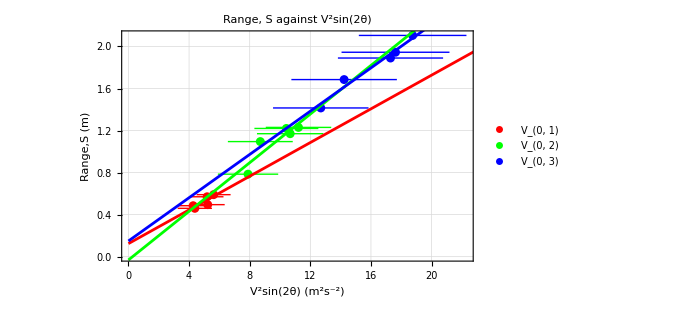
-Graphics-
V_(0, 1): y==0.0801324 x+0.124306
V_(0, 2): y==0.115682 x-0.031367
V_(0, 3): y==0.102927 x+0.149223

```mathematica
(*Define the data*)V1={{4.27,0.485},{5.19,0.570},{5.62,0.590},{5.23,0.495},{4.38,0.460}};
V2={{8.70,1.095},{10.42,1.220},{11.22,1.230},{10.67,1.170},{7.89,0.785}};
V3={{14.23,1.685},{17.29,1.890},{18.75,2.105},{17.62,1.945},{12.69,1.415}};

(*error bar*)
V1error={
{Around[4.27,1.06],Around[0.485,0.001]},{Around[5.19,1.08],Around[0.570,0.001]},{Around[5.62,1.12],Around[0.590,0.001]},{Around[5.23,1.12],Around[0.495,0.001]},{Around[4.38,1.13],Around[0.460,0.001]}};
V2error={
{Around[8.70,2.14],Around[1.095,0.001]},{Around[10.42,2.11],Around[1.220,0.001]},{Around[11.22,2.16],Around[1.230,0.001]},{Around[10.67,2.19],Around[1.170,0.001]},{Around[7.89,1.99],Around[0.785,0.001]}};
V3error={
{Around[14.23,3.48],Around[1.685,0.001]},{Around[17.29,3.47],Around[1.890,0.001]},{Around[18.75,3.55],Around[2.105,0.001]},{Around[17.62,3.56],Around[1.945,0.001]},{Around[12.69,3.15],Around[1.415,0.001]}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fit1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fit2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fit3["BestFit"]]];

(*Display the equations outside the graph with extended line plot*)
Column[{Show[ListPlot[{V1error,V2error,V3error},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,0,25},PlotStyle->{Red,Green,Blue},PlotRange->{{0,25},Automatic}],Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(V\), \(2\)]\)sin(2θ) (m^2s^-2)","Range,S (m)"},GridLines->Automatic,PlotLabel->"Range, S against \!\(\*SuperscriptBox[\(V\), \(2\)]\)sin(2θ)",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

```mathematica
G={0.08013241170122691 ,0.11568169906910444,0.10292733040824532}
g=1/G
```

{0.0801324,0.115682,0.102927}

{12.4793,8.64441,9.71559}